```mathematica
a=1;
b=0.2;
```

```mathematica
(*Define the polynomial as a function of s and x*)
poly[u_,g_]:=64*(1+4*a^2*g^2)*(1+4*b^2*g^2)-((2+2*u*g)^2-4*((1+4*a^2*g^2)+(1+4*b^2*g^2)))^2;
(*Define a function that finds the roots for a given s*)
roots[u_]:=g/. NSolve[poly[u,g]==0,g];
```

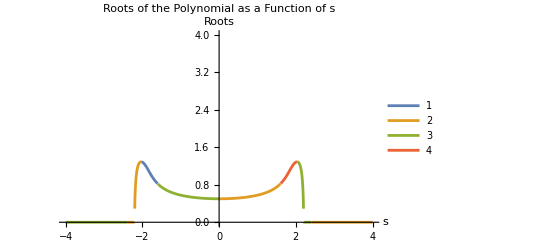

```mathematica
Plot[Evaluate[Table[Im[roots[s-10^(-4)I][[i]]],{i,4}]],{s,-4,4},PlotLegends->Automatic,AxesLabel->{"s","Roots"},PlotLabel->"Roots of the Polynomial as a Function of s", PlotRange->{0,4}]
```